List

{{PassengerId,Survived,Pclass,Name,Sex,Age,SibSp,Parch,Ticket,Fare,Cabin,Embarked},{1,0,3,Braund, Mr. Owen Harris,male,22,1,0,A/5 21171,7.25,,S},{2,1,1,Cumings, Mrs. John Bradley (Florence Briggs Thayer),female,38,1,0,PC 17599,71.2833,C85,C},{3,1,3,Heikkinen, Miss. Laina,female,26,0,0,STON/O2. 3101282,7.925,,S},{4,1,1,Futrelle, Mrs. Jacques Heath (Lily May Peel),female,35,1,0,113803,53.1,C123,S}}

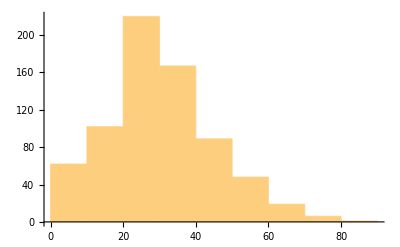

```mathematica
(* Step 1: Import Data *)
titanicData = Import["https://docs.google.com/spreadsheets/d/13BbdPizP14awpyGR_B1m0xkhHD_k9O0jnVADoq1szeU/export?format=csv&gid=1656516277"];

(* Step 2: Check the structure of the data *)
Head[titanicData]  (* Should be List *)
Take[titanicData, 5]  (* Check the first few rows *)

(* Step 3: Find the index of the "Age" column *)
ageIndex = Position[First[titanicData], "Age"][[1, 1]];

(* Step 4: Extract ages, skipping the header row *)
ages = ToExpression[titanicData[[2 ;;, ageIndex]]]; (* Converts strings to numbers *)

(* Step 5: Remove missing values *)
cleanAges = DeleteCases[ages, _String | "" | Missing[]];

(* Step 6: Select only numerical values *)
numericAges = Select[cleanAges, NumberQ];

(* Step 7: Calculate the median age *)
medianAge = Median[numericAges];

(* Step 8: Plot the histogram *)
Histogram[numericAges, "Sturges"]
```

```mathematica
(* Step 1: Calculate Descriptive Statistics for Age and Fare *)

(* Descriptive Statistics for Age *)
meanAge = Mean[numericAges];
medianAge = Median[numericAges];
stdDevAge = StandardDeviation[numericAges];
modeAge = Commonest[numericAges];

(* Descriptive Statistics for Fare *)
fareIndex = Position[First[titanicData], "Fare"][[1, 1]];
fares = ToExpression[titanicData[[2 ;;, fareIndex]]];
cleanFares = DeleteCases[fares, _String | "" | Missing[]];
numericFares = Select[cleanFares, NumberQ];

meanFare = Mean[numericFares];
medianFare = Median[numericFares];
stdDevFare = StandardDeviation[numericFares];
modeFare = Commonest[numericFares];

(* Display Statistics *)
{meanAge, medianAge, stdDevAge, modeAge}
{meanFare, medianFare, stdDevFare, modeFare}
```

{29.6991,28,14.5265,{24}}

{32.2042,14.4542,49.6934,{8.05}}

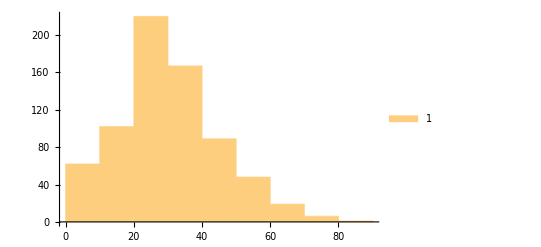

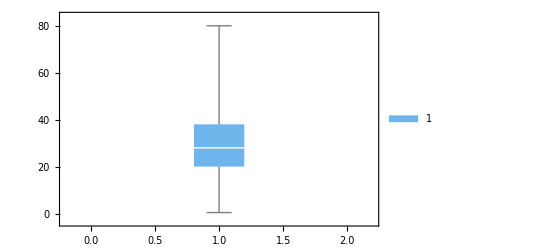

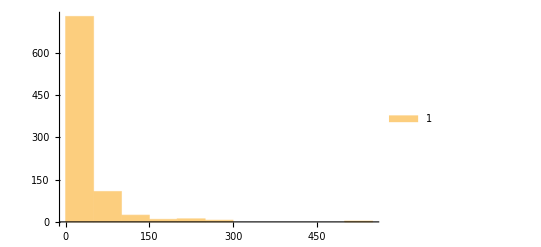

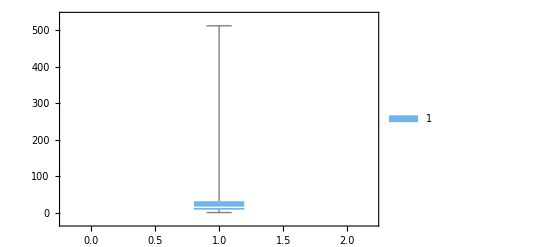

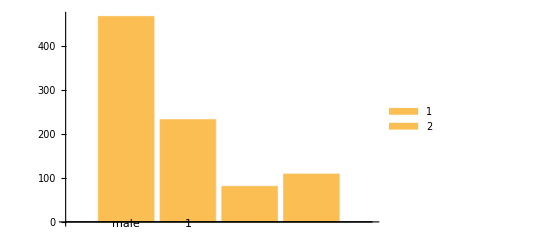

```mathematica
(* Age Distribution *)
Histogram[numericAges, "Sturges", ChartLegends -> {"Age"}]
BoxWhiskerChart[numericAges, ChartLegends -> {"Age"}, ChartStyle -> "Pastel"]

(* Fare Distribution *)
Histogram[numericFares, "Sturges", ChartLegends -> {"Fare"}]
BoxWhiskerChart[numericFares, ChartLegends -> {"Fare"}, ChartStyle -> "Pastel"]

(* Survival Rates by Gender *)
sexIndex = Position[First[titanicData], "Sex"][[1, 1]];
gender = titanicData[[2 ;;, sexIndex]];
survivedIndex = Position[First[titanicData], "Survived"][[1, 1]];
survived = ToExpression[titanicData[[2 ;;, survivedIndex]]];
genderSurvival = Tally[Transpose[{gender, survived}]];
BarChart[genderSurvival[[All, 2]], ChartLabels -> genderSurvival[[All, 1]], ChartLegends -> {"Not Survived", "Survived"}]
```

```mathematica
(* Step 1: Load Titanic Dataset *)
titanicData = ExampleData[{"Dataset", "Titanic"}];

(* Step 2: Data Cleaning - Remove rows with any missing values *)
titanicDataCleaned = Select[titanicData, FreeQ[#, Missing[]] &];

(* Step 3: Extract relevant columns *)
passengerClass = titanicDataCleaned[[All, "Pclass"]];
gender = If[# == "male", 1, 0] & /@ titanicDataCleaned[[All, "Sex"]];
survived = titanicDataCleaned[[All, "Survived"]];
age = titanicDataCleaned[[All, "Age"]];
sibsp = titanicDataCleaned[[All, "SibSp"]];
parch = titanicDataCleaned[[All, "Parch"]];

(* Step 4: Feature Engineering - Create FamilySize feature *)
familySize = sibsp + parch + 1;

(* Step 5: Remove rows with missing Age values *)
validIndices = Position[age, _?(NumberQ)];
cleanPassengerClass = Extract[passengerClass, validIndices];
cleanGender = Extract[gender, validIndices];
cleanSurvived = Extract[survived, validIndices];
cleanAges = Extract[age, validIndices];
cleanFamilySize = Extract[familySize, validIndices];

(* Step 6: Combine features *)
features = Transpose[{cleanAges, cleanPassengerClass, cleanGender, cleanFamilySize}];
labels = cleanSurvived;

(* Step 7: Ensure features and labels have the same length *)
If[Length[features] === Length[labels],
    (* Step 8: Prepare training data *)
    trainingData = MapThread[Rule, {features, labels}];
    
    (* Step 9: Train the model using Logistic Regression *)
    model = Classify[trainingData, Method -> "LogisticRegression"];
    
    (* Step 10: Evaluate model on a new data point {age, class, gender, familySize} *)
    Classify[model, {22, 3, 1, 1}],
    Print["Features and labels are not of the same length."]
]
```

Classify[Classify[{},Method→LogisticRegression],{22,3,1,1}]